```mathematica
HiPower = {{2.83529,1},{.63617,.987},{.44179,.974},{.19635,.908},{.12566,.822},{.07069,.614},{.04909,.494},{.03142,.346},{.01767,.215},{.0095,.126}};
```

```mathematica
MedPower = {{2.83529,1},{.63617,.995},{.44179,.963},{.19635,.916},{.12566,.858},{.07069,.670},{.04909,.538},{.03142,.365},{.01767,.241},{.00933,.140}};
```

```mathematica
LowPower = {{2.83529,1},{.65899,.994},{.44179,.981},{.19635,.933},{.12566,.889},{.07069,.804},{.04909,.674},{.03173,.542},{.01767,.336},{.0095,.21}};
```

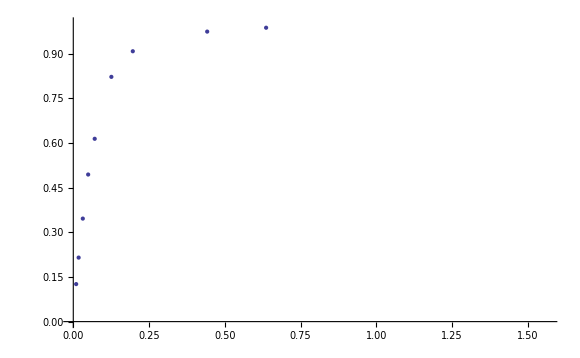

```mathematica
ListPlot[{HiPower},PlotRange->Automatic]
```

```mathematica
Gauss[x_,y_, x0_, y0_] := 1/(σ*σ*Pi*2)* Exp[-((x-x0)^2/(2σ^2)+(y-y0)^2/(2σ^2))];
```

```mathematica
Integrate[a-Sqrt[x^2+y^2],{x,-a,a},{y,-Sqrt[a^2-x^2],Sqrt[a^2-x^2]}]
```

ConditionalExpression[(a^3 π)/3,a>0]

```mathematica
Gauss[x,y,0,0]/.{x->Sqrt[r^2-y^2],y->Sqrt[r^2-x^2]}//Simplify
```

(ⅇ^((-2 r^2+x^2+y^2)/(2 σ^2)))/(2 π σ^2)

```mathematica
Integrate[r*Gauss[],{r,0,a},{θ,0,2Pi}]
```

(a^3 π)/3